```mathematica
Quit
(*PROLATE*)
```

```mathematica
g[v_,e_]:=Sqrt[1-e^2*(Cos[v])^2]
```

```mathematica
Hreq[n_,e_]:=Integrate[g[v,e]*Sin[v]*LegendreP[n,Cos[v]],{v,0,π}]
```

```mathematica
Assuming[0<e<1,Hreq[0,e]]
```

√(1-e^2)+ArcSin[e]/e

```mathematica
Assuming[e∈Reals && 0<e<1&&n∈Integers&&n≥0,ProlateQreq[n_,e_]:=1/(2*LegendreP[n,0])*Integrate[LegendreP[n,x]/(√((1/e)^2-1+x^2)),{x,-1,1}]]
```

```mathematica
Prolateop:=Sum[(2n+1)/2* FullSimplify[ProlateQreq[n,e]*LegendreP[n,1/e]]*Hreq[n,e]*Hreq[n,e],{n,0,0,2}]
```

```mathematica
Assuming[0<e<1 && n ∈ Integers, Prolateop]
```

1/2 (√(1-e^2)+ArcSin[e]/e)^2 ArcTanh[e]

```mathematica
ProlateU0[e_]:=1/4 (√(1-e^2)+ArcSin[e]/e)^2 Log[(1+e)/(1-e)]
```

```mathematica
ProlateU2[e_]:=1/4 (√(1-e^2)+ArcSin[e]/e)^2 Log[(1+e)/(1-e)]+1/(512 e^10)5 (-3+e^2) (e √(1-e^2) (-3+2 e^2)+(3-4 e^2) ArcSin[e])^2 (3 (-1+e^2) ArcSinh[e/(√(1-e^2))]+e (3+e Log[-1+2/(1+e)]))
```

```mathematica
ProlateU4[e_]:=1/(1572864 e^18)(35-30 e^2+3 e^4) (e √(1-e^2) (-105+110 e^2-8 e^4)+3 (35-60 e^2+24 e^4) ArcSin[e])^2 (5 e (-21+11 e^2)+3 (35-30 e^2+3 e^4) ArcSinh[e/(√(1-e^2))])+1/4 (√(1-e^2)+ArcSin[e]/e)^2 Log[(1+e)/(1-e)]+1/(512 e^10)5 (-3+e^2) (e √(1-e^2) (-3+2 e^2)+(3-4 e^2) ArcSin[e])^2 (3 (-1+e^2) ArcSinh[e/(√(1-e^2))]+e (3+e Log[-1+2/(1+e)]))
```

```mathematica
ProlateU6[e_]:=1/(1572864 e^18)(35-30 e^2+3 e^4) (e √(1-e^2) (-105+110 e^2-8 e^4)+3 (35-60 e^2+24 e^4) ArcSin[e])^2 (5 e (-21+11 e^2)+3 (35-30 e^2+3 e^4) ArcSinh[e/(√(1-e^2))])+1/(2684354560 e^26)13 (e √(1-e^2) (-1155+1750 e^2-616 e^4+16 e^6)-5 (-231+8 e^2 (63-42 e^2+8 e^4)) ArcSin[e])^2 (7 e (165-170 e^2+33 e^4) (-231+5 e^2 (63-21 e^2+e^4))+5 (231-5 e^2 (63-21 e^2+e^4))^2 ArcSinh[e/(√(1-e^2))])+1/4 (√(1-e^2)+ArcSin[e]/e)^2 Log[(1+e)/(1-e)]+1/(512 e^10)5 (-3+e^2) (e √(1-e^2) (-3+2 e^2)+(3-4 e^2) ArcSin[e])^2 (3 (-1+e^2) ArcSinh[e/(√(1-e^2))]+e (3+e Log[-1+2/(1+e)]))
```

```mathematica
ProlateU8[e_]:=FullSimplify[1/(1572864 e^18)(35-30 e^2+3 e^4) (e √(1-e^2) (-105+110 e^2-8 e^4)+3 (35-60 e^2+24 e^4) ArcSin[e])^2 (5 e (-21+11 e^2)+3 (35-30 e^2+3 e^4) ArcSinh[e/(√(1-e^2))])+1/(2684354560 e^26)13 (e √(1-e^2) (-1155+1750 e^2-616 e^4+16 e^6)-5 (-231+8 e^2 (63-42 e^2+8 e^4)) ArcSin[e])^2 (7 e (165-170 e^2+33 e^4) (-231+5 e^2 (63-21 e^2+e^4))+5 (231-5 e^2 (63-21 e^2+e^4))^2 ArcSinh[e/(√(1-e^2))])+1/(307863255777280 e^34)17 (6435+7 e^2 (-1716+5 e^2 (198-36 e^2+e^4))) (e √(1-e^2) (-45045+90090 e^2-54824 e^4+9872 e^6-128 e^8)+35 (1287+8 e^2 (-429+4 e^2 (99-36 e^2+4 e^4))) ArcSin[e])^2 (e (-225225+345345 e^2-147455 e^4+15159 e^6)+35 (6435+7 e^2 (-1716+5 e^2 (198-36 e^2+e^4))) ArcSinh[e/(√(1-e^2))])+1/4 (√(1-e^2)+ArcSin[e]/e)^2 Log[(1+e)/(1-e)]+1/(512 e^10)5 (-3+e^2) (e √(1-e^2) (-3+2 e^2)+(3-4 e^2) ArcSin[e])^2 (3 (-1+e^2) ArcSinh[e/(√(1-e^2))]+e (3+e Log[-1+2/(1+e)]))]
```

```mathematica
ProlateArea[e_,a_]:=2π*a^2*√(1-e^2)*(√(1-e^2)+ArcSin[e]/e)
```

```mathematica
Limit[ProlateArea[e,1],e->0]
```

4 π

```mathematica
Limit[ProlateArea[e,1],e->1]
```

0

```mathematica
Limit[ProlateU0[e],e->1]
```

∞

```mathematica
Prolateσ[Q_,e_,a_]:=Q/ProlateArea[e,a]
```

```mathematica
ProlateU[e_,a_,Q_]:=4*π^2*(Prolateσ[Q,e,a])^2*a^3*(1-e^2)/e*ProlateU6[e]
```

```mathematica
Limit[ProlateU[e,a,Q],e->0]
```

Q^2/(2 a)

```mathematica
Limit[ProlateU[e,a,Q],e->1]
```

(Q^2 ∞)/a

```mathematica
ProlateVfixa[e_,R0_]:=R0/((1-e^2)^(1/3))
```

```mathematica
HomoProlateUVfix[e_,R0_,Q_]:=ProlateU[e,ProlateVfixa[e,R0],Q]
```

```mathematica
Limit[HomoProlateUVfix[e,R0,Q],e->1]
```

0

```mathematica
ProlateAfixa[e_,R0_]:= R0*√(2/(1-e^2+(√(1-e^2))/e ArcSin[e]))
```

```mathematica
HomoProlateUAfix[e_,R0_,Q_]:=ProlateU[e,ProlateAfixa[e,R0],Q]
```

```mathematica
Limit[HomoProlateUAfix[e,1,1],e->1]
```

0

```mathematica
eprolate[λ_]:=√(1-(1/λ)^2)
```

```mathematica
CondProlateU[e_,c_,Q_]:=Q^2/(2c*e)*ArcTanh[e]
```

```mathematica
CondProlateUVfix[e_,R0_,Q_]:=CondProlateU[e,ProlateVfixa[e,R0],Q]
```

```mathematica
Limit[CondProlateUVfix[d,R0,Q],d->1]
```

0

```mathematica
CondProlateUAfix[e_,R0_,Q_]:=CondProlateU[e,ProlateAfixa[e,R0],Q]
```

```mathematica
Limit[CondProlateUAfix[d,R0,Q],d->0]
```

Q^2/(2 R0)

```mathematica
(*OBLATE*)
```

```mathematica
f[v_,e_]:=Sqrt[1-e^2*(Sin[v])^2]
```

```mathematica
Ireq[n_,e_]:=Integrate[f[v,e]*Sin[v]*LegendreP[n,Cos[v]],{v,0,π}]
```

```mathematica
Assuming[e∈Reals && 0<e<1&&n∈Integers&&n≥0,OblateQreq[n_,e_]:=1/(2*ⅈ*LegendreP[n,0])*Integrate[LegendreP[n,x]/(√((1/e)^2-x^2)),{x,-1,1}]]
```

```mathematica
Oblateop:=Sum[(2n+1)/2* FullSimplify[(OblateQreq[n,e]*LegendreP[n,(ⅈ*√(1-e^2))/e])/(ⅈ*e)]*(Ireq[n,e])^2,{n,0,0,2}]
```

```mathematica
Assuming[0<e<1 && n ∈ Integers, Oblateop]
```

-((1+(ⅈ (-1+e^2) π)/(2 e)+(-1/e+e) ArcCoth[e])^2 ArcSin[e])/(2 e)

```mathematica
OblateU0[e_]:=-(ArcSin[e] (1+(1/e-e) ArcTanh[e])^2)/(2 e)
```

```mathematica
OblateU2[e_]:=-(ArcSin[e] (1+(1/e-e) ArcTanh[e])^2)/(2 e)-1/(512 e^11)5 (-3+2 e^2) (3 e √(1-e^2)+(-3+2 e^2) ArcSin[e]) (-e (-3+e^2)+(-3+2 e^2+e^4) ArcTanh[e])^2
```

```mathematica
OblateU4[e_]:=-(ArcSin[e] (1+(1/e-e) ArcTanh[e])^2)/(2 e)-1/(512 e^11)5 (-3+2 e^2) (3 e √(1-e^2)+(-3+2 e^2) ArcSin[e]) (-e (-3+e^2)+(-3+2 e^2+e^4) ArcTanh[e])^2-1/(6291456 e^19)(35+8 e^2 (-5+e^2)) (5 e √(1-e^2) (-21+10 e^2)+3 (35+8 e^2 (-5+e^2)) ArcSin[e]) (-210 e+200 e^3-6 e^5+6 (35-45 e^2+9 e^4+e^6) ArcTanh[e])^2
```

```mathematica
OblateU6[e_]:=-(ArcSin[e] (1+(1/e-e) ArcTanh[e])^2)/(2 e)-1/(512 e^11)5 (-3+2 e^2) (3 e √(1-e^2)+(-3+2 e^2) ArcSin[e]) (-e (-3+e^2)+(-3+2 e^2+e^4) ArcTanh[e])^2-1/(6291456 e^19)(35+8 e^2 (-5+e^2)) (5 e √(1-e^2) (-21+10 e^2)+3 (35+8 e^2 (-5+e^2)) ArcSin[e]) (-210 e+200 e^3-6 e^5+6 (35-45 e^2+9 e^4+e^6) ArcTanh[e])^2 -1/(2684354560 e^27)13 (-231+378 e^2-168 e^4+16 e^6) (7 e √(1-e^2) (165-160 e^2+28 e^4)+5 (-231+378 e^2-168 e^4+16 e^6) ArcSin[e]) (1155 e-1715 e^3+581 e^5-5 e^7+5 (-1+e) (1+e) (231-189 e^2+21 e^4+e^6) ArcTanh[e])^2
```

```mathematica
OblateArea[e_,a_]:=2*π*a*a*(1+(1-e*e)/e ArcTanh[e])
```

```mathematica
Oblateσ[Q_,e_,a_]:=Q/OblateArea[e,a]
```

```mathematica
OblateU[e_,a_,Q_]:=-4*π^2*(Oblateσ[Q,e,a])^2*a^3*OblateU6[e]
```

```mathematica
Limit[OblateU[e,a,Q],e->1]
```

(1133125 π Q^2)/(4194304 a)

```mathematica
N[8/(3π)-(1133125 π)/4194304]
```

0.0000998103

```mathematica
OblateVfixa[e_,R0_]:=R0/((1-e^2)^(1/6))
```

```mathematica
HomoOblateUVfix[e_,R0_,Q_]:=OblateU[e,OblateVfixa[e,R0],Q]
```

```mathematica
OblateAfixa[e_,R0_]:=R0*√(2/(1+(1-e*e)/e ArcTanh[e]))
```

```mathematica
HomoOblateUAfix[e_,R0_,Q_]:=OblateU[e,OblateAfixa[e,R0],Q]
```

```mathematica
Limit[HomoOblateUVfix[e,R0,Q],e->1]
```

0

```mathematica
Limit[HomoOblateUAfix[e,R0,Q],e->1]
```

(1133125 π Q^2)/(4194304 √2 R0)

```mathematica
N[(1133125 π)/(4194304 √2)]
```

0.60014

```mathematica
eoblate[λ_]:=√(1-λ^2)
```

```mathematica
CondOblateU[e_,a_,Q_]:=Assuming[e>0,Q^2/(2a*e)ArcTan[e/(√(1-e^2))]]
```

```mathematica
CondOblateUVfix[e_,R0_,Q_]:=CondOblateU[e,OblateVfixa[e,R0],Q]
```

```mathematica
CondOblateUAfix[e_,R0_,Q_]:=CondOblateU[e,OblateAfixa[e,R0],Q]
```

```mathematica
(*Coulomb energy of a spheroidal shell for charges uniformly spread around. Function of c/a where c is the semi z-axis length, and a is semi x-axis length.
c/a -> 0 is a disc (oblate), c/a -> 1 is a sphere, c/a -> ∞ is a thin rod (prolate)*)
```

```mathematica
HomoSpheroidUVfix[λ_,R0_,Q_]:=If[λ<1,HomoOblateUVfix[eoblate[λ],R0,Q],HomoProlateUVfix[eprolate[λ],R0,Q]] (* Volume is fixed *)
```

```mathematica
HomoSpheroidUAfix[λ_,R0_,Q_]:=If[λ<1,HomoOblateUAfix[eoblate[λ],R0,Q],HomoProlateUAfix[eprolate[λ],R0,Q]] (* Area is fixed *)
```

```mathematica
(*Coulomb energy of a spheroidal shell for conducting case. Function of c/a where c is the semi z-axis length, and a is semi x-axis length.
c/a -> 0 is a disc (oblate), c/a -> 1 is a sphere, c/a -> ∞ is a thin rod (prolate)*)
```

```mathematica
CondSpheroidUVfix[λ_,R0_,Q_]:=If[λ<1,CondOblateUVfix[eoblate[λ],R0,Q],CondProlateUVfix[eprolate[λ],R0,Q]] (* Volume is fixed *)
```

```mathematica
CondSpheroidUAfix[λ_,R0_,Q_]:=If[λ<1,CondOblateUAfix[eoblate[λ],R0,Q],CondProlateUAfix[eprolate[λ],R0,Q]] (* Area is fixed *)
```

```mathematica
Limit[HomoSpheroidUAfix[d,R0,Q],d->0]
```

(1133125 π Q^2)/(4194304 √2 R0)

```mathematica
Limit[CondOblateUVfix[d,R0,Q],d->1]
```

0

```mathematica
Limit[CondSpheroidUAfix[λ,R0,Q],λ->0]
```

(π Q^2)/(4 √2 R0)

```mathematica
Limit[HomoSpheroidUAfix[λ,R0,Q],λ->∞]
```

0

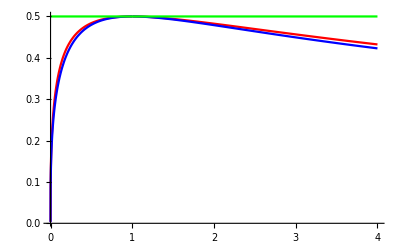

```mathematica
Plot[{HomoSpheroidUVfix[λ,1,1],CondSpheroidUVfix[λ,1,1],0.5},{λ,0,4},PlotRange->{All,All},PlotStyle->{Red,Blue,Green}]
```

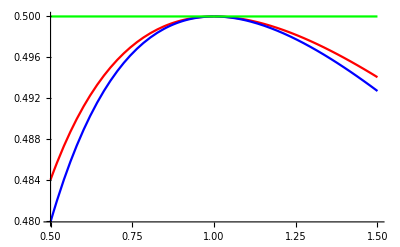

```mathematica
Plot[{HomoSpheroidUVfix[λ,1,1],CondSpheroidUVfix[λ,1,1],0.5},{λ,0.5,1.5},PlotRange->{All,All},PlotStyle->{Red,Blue,Green}]
```

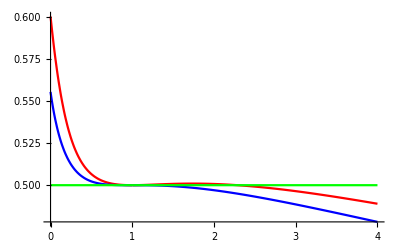

```mathematica
Plot[{HomoSpheroidUAfix[λ,1,1],CondSpheroidUAfix[λ,1,1],0.5},{λ,0,4},PlotRange->{All,All},PlotStyle->{Red,Blue,Green}]
```

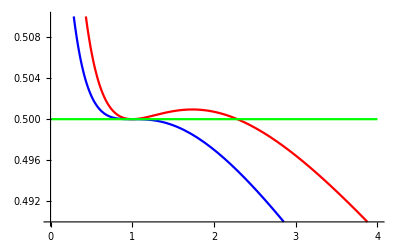

```mathematica
Plot[{HomoSpheroidUAfix[λ,1,1],CondSpheroidUAfix[λ,1,1],0.5},{λ,0,4},PlotRange->{All,{0.49,0.51}},PlotStyle->{Red,Blue,Green}]
```

```mathematica
(* Check on number of terms in expansion n = 6, n = 8 give essentially same results*)
```

```mathematica
HomoSpheroidUAfixn8[λ_,R0_,Q_]:=If[λ<1,HomoOblateUAfix[eoblate[λ],R0,Q],HomoProlateUAfix[eprolate[λ],R0,Q]] (* Area is fixed *)
```

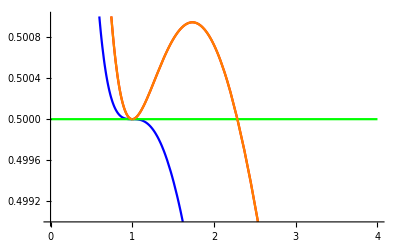

```mathematica
Plot[{HomoSpheroidUAfix[λ,1,1],CondSpheroidUAfix[λ,1,1],0.5,HomoSpheroidUAfixn8[λ,1,1]},{λ,0,4},PlotRange->{All,{0.499,0.501}},PlotStyle->{Red,Blue,Green,Orange,Dotted}]
```

```mathematica
Table[HomoSpheroidUAfix[λ,1,1],{λ,2,4,0.1}](*I think this is 6 terms*)
```

{0.500722,0.500524,0.500267,0.499954,0.499587,0.49917,0.498707,0.498201,0.497655,0.497073,0.496457,0.495811,0.495136,0.494435,0.493712,0.492967,0.492204,0.491423,0.490626,0.489816,0.488994}

```mathematica
Table[HomoSpheroidUAfixn8[λ,1,1],{λ,2,4,0.1}]
```

{0.500722,0.500524,0.500267,0.499954,0.499587,0.49917,0.498707,0.498201,0.497655,0.497073,0.496457,0.495811,0.495136,0.494435,0.493712,0.492967,0.492204,0.491423,0.490626,0.489816,0.488994}

```mathematica
(*Outputing data for gnuplot*)
```

```mathematica
filelambda = Column[Table[λ,{λ,0.001,4,0.001}]];
```

```mathematica
(**** HVfix= Column[Table[HomoSpheroidUVfix[λ,1,1],{λ,0.001,4,0.001}]]; need to eliminate 1/0 points ****)
```